```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap1D[];
sizes={256};
timeStep=0.001;
k=-0.5;
contactInteractionFactor=4 Pi k;
max=5ho;
min=-max;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{256} | 1 | 256 | {5} | {-5} | {2/51} | {(51 π)/256} | {(51 π)/2}

```mathematica
moments:=Join[Array[mean,dim],Array[sigma,dim],Table[mom[n,4],{n,dim}],Table[mom[n,6],{n,dim}],{norm}];
momentslegend:=Join[Table["mean"<>dir[i],{i,dim}],Table["sigma"<>dir[i],{i,dim}],
Table["mom4"<>dir[i],{i,dim}],Table["mom6"<>dir[i],{i,dim}],{"norm"}];
```

```mathematica
calcAllTable
p1=plotProjectionsOpts[PlotStyle->Orange];
```

time | energies | moments | misc
(0) | (total | -0.753314
kinetic | 0.25
potential | 0.25
contact | -1.25331
virial | -1.25331) | (meanX | 0
sigmaX | 0.707107
mom4X | 0.75
mom6X | 1.875
norm | 1.) | (steps | 0
A0 | 0.751125)

```mathematica
myPrint=Null&;
AbsoluteTiming[evolve["ite",5,10]]
```

{0.673266,Null}

time | energies | moments | misc
(5.) | (total | -1.60438
kinetic | 1.70079
potential | 0.0398038
contact | -3.34497
virial | -0.0229954) | (meanX | 0
sigmaX | 0.282148
mom4X | 0.0256647
mom6X | 0.0178232
norm | 1.) | (steps | 5000
A0 | 1.26157)

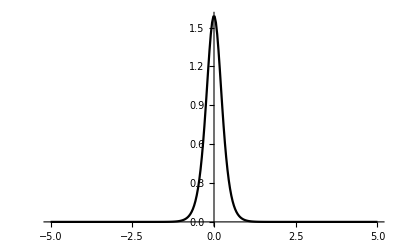

```mathematica
calcAllTable
p2=plotProjectionsOpts[PlotStyle->Black]
```

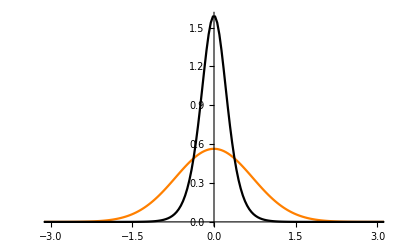

```mathematica
Show[p1,p2,PlotRange->{{-3,3},All}]
```

```mathematica
reportEnergies
```

time | total | kinetic | potential | contact | virial
0 | -0.753314 | 0.25 | 0.25 | -1.25331 | -1.25331
0.5 | -1.50661 | 1.04702 | 0.0684981 | -2.62213 | -0.665077
1. | -1.60233 | 1.61109 | 0.0424031 | -3.25583 | -0.118448
1.5 | -1.60431 | 1.69192 | 0.0400481 | -3.33627 | -0.0325352
2. | -1.60437 | 1.69994 | 0.039827 | -3.34414 | -0.0239071
2.5 | -1.60438 | 1.70071 | 0.039806 | -3.34489 | -0.0230821
3. | -1.60438 | 1.70078 | 0.039804 | -3.34496 | -0.0230036
3.5 | -1.60438 | 1.70079 | 0.0398039 | -3.34497 | -0.0229962
4. | -1.60438 | 1.70079 | 0.0398038 | -3.34497 | -0.0229955
4.5 | -1.60438 | 1.70079 | 0.0398038 | -3.34497 | -0.0229954
5. | -1.60438 | 1.70079 | 0.0398038 | -3.34497 | -0.0229954

```mathematica
threeBodyLosses=True;
lossRate=0.05;
threeBodyLossesFactor=(-I/2)lossRate;
tmax=10;
reset;
myPrint=Null&;
AbsoluteTiming[evolve["rte",tmax,100,100]]
```

{5.91154,Null}

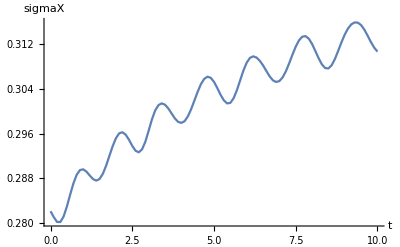

```mathematica
plotM["sigmaX"]
```

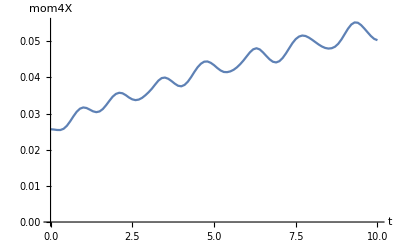

```mathematica
plotM["mom4X"]
```

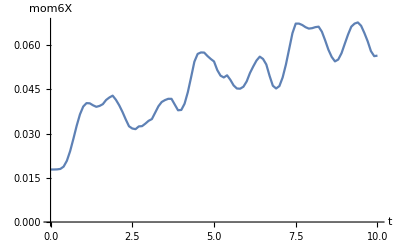

```mathematica
plotM["mom6X"]
```

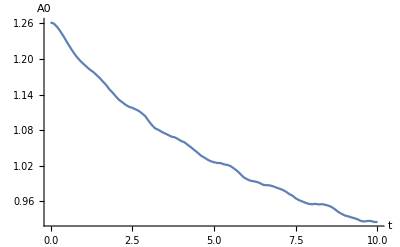

```mathematica
plotM["A0"]
```

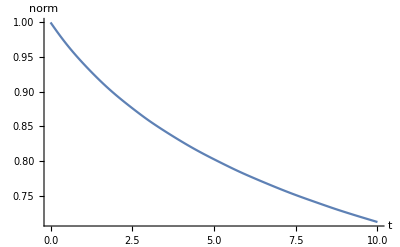

```mathematica
plotM["norm"]
```

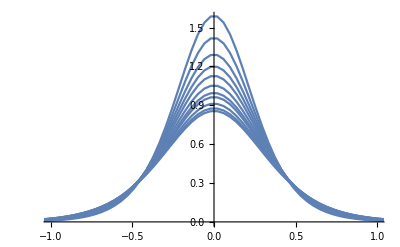

```mathematica
Show[lplots[[1;;;;10,2]],PlotRange->{{-1,1},All}]
```